```mathematica
ClearAll["Global`*"];
ClearAll[m];
```

```mathematica
ExtractData[file_]:=Module[{data,shadow,measure,lines,line,xmin,xmax,ymin,ymax,xc,yc,Dc,Dx,Dy,newLine,polarLine,r,rbar,σr,LHratio,area},
data=Import[file];
shadow=EdgeDetect[data,30];(*should test carefully before changing it*)
line=ImageValuePositions[shadow,1]-1024;
{xmin,xmax}=MinMax[line⟦All,1⟧];
{ymin,ymax}=MinMax[line⟦All,2⟧];
{xc,yc}={(xmin+xmax)/2,(ymin+ymax)/2};
Dc=Abs@xc;
{Dx,Dy}={xmax-xmin,ymax-ymin};
LHratio=Dx/Dy;
newLine=Union[line,SameTest->(Norm[#1-#2]<5&)];(*remove very close points*)
polarLine=DeleteDuplicates[{ArcTan[#⟦1⟧-xc,#⟦2⟧],√((#⟦1⟧-xc)^2+(#⟦2⟧)^2)}&/@newLine,#1⟦1⟧==#2⟦1⟧&];
polarLine=Join[Select[SortBy[polarLine,First],#⟦1⟧>0&],{#⟦1⟧+2π,#⟦2⟧}&/@Select[SortBy[polarLine,First],#⟦1⟧<0&]];
r02pi=polarLine[[1,2]];
AppendTo[polarLine,{0,r02pi}];
AppendTo[polarLine,{2π,r02pi}];
r=Interpolation[polarLine,InterpolationOrder->0];
rbar=NIntegrate[r[α]/(2π),{α,0,2π}];
σr=√NIntegrate[(r[α]-rbar)^2/(2π),{α,0,2π}];
area=NIntegrate[1/2 r[α]^2,{α,0,2π}];
{line,xmin,xmax,ymin,ymax,xc,yc,newLine,polarLine,r,Dc,Dx,Dy,LHratio,rbar,σr,area}];
```

```mathematica
FNs=FileNames[FileNameJoin[{NotebookDirectory[],"KerrQED*_bw.png"}]]
```

{D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-10_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-11_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-1_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-2_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-3_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-4_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-5_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-6_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-7_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-8_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-9_bw.png}

```mathematica
FNtab=Table[If[m≤9,FNs[[m+2]],FNs[[m-9]]],{m,1,11}]
```

{D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-1_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-2_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-3_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-4_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-5_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-6_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-7_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-8_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-9_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-10_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\A\KerrQED-11_bw.png}

```mathematica
shapedata=Map[ExtractData,FNtab];
shrink=Table[shapedata[[m,-1]]/shapedata[[1,-1]],{m,1,11}]
```

{1.,0.980967,0.960978,0.93941,0.916346,0.891178,0.863709,0.831926,0.795631,0.74892,0.669529}

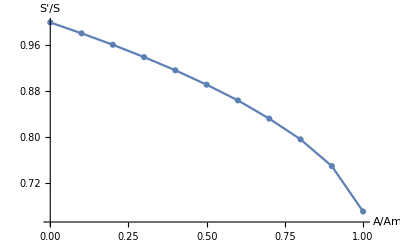

```mathematica
ListLinePlot[Table[{0.1(m-1),shrink[[m]]},{m,1,11}],AxesLabel->{"A/Am","S'/S"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
σk=Table[√(1/(2π)NIntegrate[((shapedata[[m,10]][α]-shapedata[[1,10]][α])/(shapedata[[1,10]][α]))^2,{α,0,2π}]),{m,1,11}]
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

{0.,0.0100858,0.0203564,0.0316012,0.0439029,0.0575771,0.0726889,0.0904872,0.111484,0.139395,0.191167}

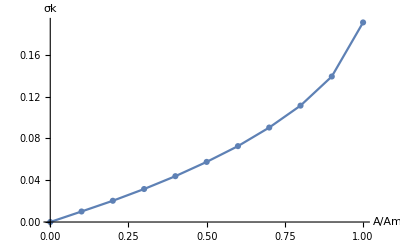

```mathematica
ListLinePlot[Table[{0.1(m-1),σk[[m]]},{m,1,11}],AxesLabel->{"A/Am","σk"},PlotRange->All,PlotMarkers->Automatic]
```